```mathematica
ClearAll["Global`*"]
```

```mathematica
table0571 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,57_1.txt",{"Table", "Data"}];
table0571[[All,1]]=table0571[[All,1]]-table0571[[1,1]];
table0571[[All,2]]=((table0571[[All,2]]+0.002)/(0.0043×0.01853));
table0571[[All,2]]=table0571[[All,2]]-Min[table0571[[All,2]]];
```

```mathematica
table0572 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,57_2.txt",{"Table", "Data"}];
table0572[[All,1]]=table0572[[All,1]]-table0572[[1,1]];
table0572[[All,2]]=((table0572[[All,2]]+0.002)/(0.0043×0.01853));
table0572[[All,2]]=table0572[[All,2]]-Min[table0572[[All,2]]];
```

```mathematica
table0573 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,57_3.txt",{"Table", "Data"}];
table0573[[All,1]]=table0573[[All,1]]-table0573[[1,1]];
table0573[[All,2]]=((table0573[[All,2]]+0.002)/(0.0043×0.01853));
table0573[[All,2]]=table0573[[All,2]]-Min[table0573[[All,2]]];
```

```mathematica
table0574 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,57_4.txt",{"Table", "Data"}];
table0574[[All,1]]=table0574[[All,1]]-table0574[[1,1]];
table0574[[All,2]]=((table0574[[All,2]]+0.002)/(0.0043×0.01853));
table0574[[All,2]]=table0574[[All,2]]-Min[table0574[[All,2]]];
```

```mathematica
table0575 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,57_5.txt",{"Table", "Data"}];
table0575[[All,1]]=table0575[[All,1]]-table0575[[1,1]];
table0575[[All,2]]=((table0575[[All,2]]+0.002)/(0.0043×0.01853));
table0575[[All,2]]=table0575[[All,2]]-Min[table0575[[All,2]]];
```

```mathematica
Export["table0571.dat",table0571];Export["table0572.dat",table0572];Export["table0573.dat",table0573];Export["table0574.dat",table0574];Export["table0575.dat",table0575];
```

```mathematica
T[k_,T0_,Tout_,t_]:=Tout+(T0-Tout)×Exp[-k×t]
```

```mathematica
fit0571=FindFit[table0571,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.0970477,T0→31.6815,Tout→-0.404215}

```mathematica
fit0572=FindFit[table0572,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.104198,T0→30.8081,Tout→0.527934}

```mathematica
fit0573=FindFit[table0573,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.137273,T0→38.048,Tout→0.826458}

```mathematica
fit0574=FindFit[table0574,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.113977,T0→28.5281,Tout→0.387105}

```mathematica
fit0575=FindFit[table0575,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.109866,T0→32.8876,Tout→0.593218}

```mathematica
k0571=Mean[{k/.fit0571,k/.fit0572,k/.fit0573,k/.fit0574,k/.fit0575}]
```

0.112472

```mathematica
StandardDeviation[{k/.fit0571,k/.fit0572,k/.fit0573,k/.fit0574,k/.fit0575}]
```

0.0152521

```mathematica
T0set={Tout/.fit0571,Tout/.fit0572,Tout/.fit0573,Tout/.fit0574,Tout/.fit0575}
```

{-0.404215,0.527934,0.826458,0.387105,0.593218}

```mathematica
Mean[T0set]
```

0.3861

```mathematica
StandardDeviation[T0set]
```

0.469449

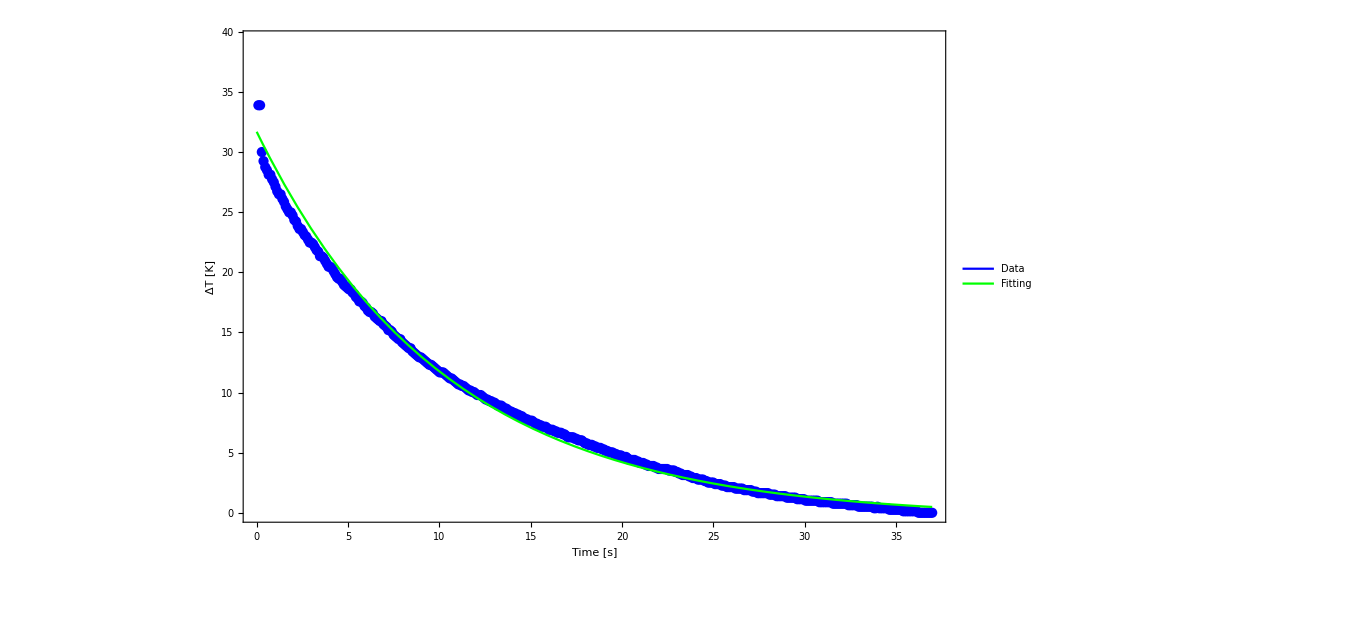

```mathematica
Legended[Show[ListPlot[table0571,PlotStyle->Blue],
Plot[T[k,T0,Tout,t]/.fit0571,{t,0,Max[table0571[[All,1]]]},PlotStyle->Green],  Frame->{True,True,False,False},FrameLabel->{"Time [s]","ΔT [K]"},ImageSize->1000, BaseStyle->{FontSize->24}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```